# Hoax News Detection by It’s Headline

## Natural Language Processing on Detecting a Hoax News using Indonesian Languages

by: Dhewa Radya | 6701011256

## Data Preparation

```mathematica
data = Import["D:\\Coding\\school\\Chula Big Data Class\\data berita jabar.csv"];
```

```mathematica
dataset = Dataset[data]
```

```mathematica
dimData = Dimensions[dataset]
```

{362,11}

```mathematica
selectedData = dataset[[2;;, {4, 7}]]
```

## Exploratory Data Analysis

### Checking the distribution of Data

```mathematica
textList = Normal[selectedData[All, {1}]];
```

```mathematica
textList = Flatten[textList];
```

```mathematica
wordList = Flatten[StringSplit /@ textList];
```

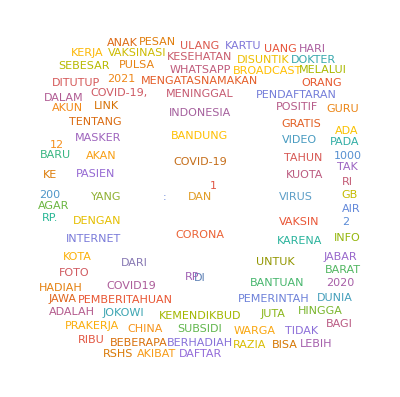

```mathematica
WordCloud[wordList]
```

```mathematica
(* Count occurrences of each status *)
statusCounts = Tally[selectedData[[All, 2]]]
```

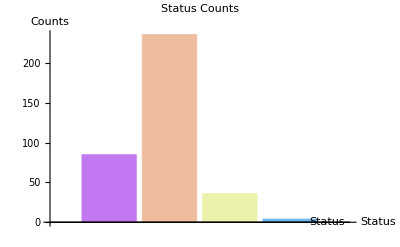

```mathematica
BarChart[statusCounts[[All, 2]], 
 ChartLabels -> Placed[{"BENAR", "DISINFORMASI", "MISINFORMASI"}, "Center"],
 ChartStyle -> "Pastel", 
 AxesLabel -> {"Status", "Counts"}, 
 PlotLabel -> "Status Counts"]
```

### Checking for Null Data

```mathematica
(* Check for empty 'judul_berita' *)
Select[selectedData, #[[1]] === "" &]
```

### Describing the Dataset

```mathematica
describeData = {
   "Count" -> Length[selectedData],
   "Unique Titles" -> Length[Union[selectedData[[All, 1]]]],
   "Unique Status" -> Length[Union[selectedData[[All, 2]]]],
   "Most Frequent Title" -> First@Commonest[selectedData[[All, 1]]],
   "Most Frequent Status" -> First@Commonest[selectedData[[All, 2]]]
   }
```

{Count→361,Unique Titles→361,Unique Status→361,Most Frequent Title→DAFTAR PRAKERJA MELALUI SITUS HTTPS://PRAKERJA.VIP,Most Frequent Status→DISINFORMASI (HOAKS)}

### Checking Duplicates

```mathematica
duplicateCounts = Tally[
   Select[selectedData[[All, 1]], Count[selectedData[[All, 1]], #] > 1 &]
   ]
```

## Data Cleaning

### Deleting Duplicates

```mathematica
cleanedData = DeleteDuplicates[selectedData]
```

```mathematica
Counts[cleanedData[[All, {2}]]]
```

### Fixing the Classification

```mathematica
cleanedData = MapAt[
   Replace[#, {"DISINFORMASI (HOAKS)" -> "HOAX", "MISINFORMASI (HOAKS)" -> "HOAX"}] &,
   cleanedData,
   {All, 2}
];
```

```mathematica
Counts[cleanedData[[All, {2}]]]
```

```mathematica
cleanedData = Select[cleanedData, #[[2]] =!= 0 &];
```

### Class Balancing

```mathematica
nSamples = 80;

dfHoax = RandomSample[
  Select[cleanedData, #[[2]] == "HOAX" &], 
  nSamples
];

dfTrue = RandomSample[
  Select[cleanedData, #[[2]] == "BENAR" &], 
  nSamples
];
```

```mathematica
cleanedData = Join[dfHoax, dfTrue];
```

## NLP Preprocessing

### Wordopt

My way to say “Word Optimization”

```mathematica
wordopt[text_String] := Module[{cleanedText = text},
  
  (* Convert text to lowercase *)
  cleanedText = ToLowerCase[cleanedText];
  
  (* Remove text within brackets *)
  cleanedText = StringReplace[cleanedText, 
    RegularExpression["\\[.*?\\]"] -> ""];
  
  (* Remove URLs *)
  cleanedText = StringReplace[cleanedText, 
    RegularExpression["https?://[\\S]+|www\\.[\\S]+"] -> ""];
  
  (* Remove HTML tags *)
  cleanedText = StringReplace[cleanedText, 
    RegularExpression["<[^>]*>"] -> ""];
  
  (* Remove HTML character codes (like &amp;) *)
  cleanedText = StringReplace[cleanedText, 
    RegularExpression["&[A-Za-z0-9]+;"] -> " "];
  
  (* Remove punctuation *)
  cleanedText = StringReplace[cleanedText, 
    RegularExpression["[^\\w\\s]"] -> ""];
  
  (* Remove extra whitespace *)
  cleanedText = StringReplace[cleanedText, 
    RegularExpression["\\s+"] -> " "];
  
  (* Remove newline characters *)
  cleanedText = StringReplace[cleanedText, "\n" -> " "];
  
  (* Remove leading/trailing whitespace *)
  cleanedText = StringTrim[cleanedText];
  
  (* Return cleaned text *)
  cleanedText
]
```

```mathematica
text = "Here's some [bracketed] text with a <b>HTML tag</b> and a URL https://example.com";
wordopt[text]
```

heres some text with a html tag and a url

```mathematica
cleanedData = MapAt[wordopt, cleanedData, {All, 1}]
```

### Tokenization

Breaking down text into individual words or tokens

```mathematica
(* Basic word tokenization *)
tokenizeBasic[text_String] := DeleteStopwords[StringSplit[text]]

(* More advanced tokenization with options *)
tokenizeAdvanced[text_String, opts:OptionsPattern[]] := Module[
    {words, minLength = OptionValue[MinWordLength]},
    
    (* Split into words *)
    words = StringSplit[text];
    
    (* Remove stopwords if specified *)
    If[OptionValue[RemoveStopwords],
        words = DeleteStopwords[words]
    ];
    
    (* Filter by minimum length if specified *)
    If[minLength > 0,
        words = Select[words, StringLength[#] >= minLength &]
    ];
    
    words
]

(* Set default options *)
Options[tokenizeAdvanced] = {
    MinWordLength -> 0,
    RemoveStopwords -> False
};

(* Function to get word frequencies *)
getWordFrequencies[words_List] := Counts[words]
```

```mathematica
text = "this is a sample text";
tokens = tokenizeBasic[text]
```

```mathematica
{"this", "is", "a","sample","text"}
```

{this,is,a,sample,text}

```mathematica
(* Assuming your data has text in column 1 and sentiment in column 2 *)
tokenizedData = Table[
    {tokenizeBasic[cleanedData[[i, 1]]], cleanedData[[i, 2]]},
    {i, Length[cleanedData]}
];

tokenizedData = Dataset[tokenizedData];
```

### StopWords

Removing common words that don’t carry much meaning (e.g., “the,” “and,” “of”).

```mathematica
(* Define Indonesian stopwords *)
indonesianStopwords = {
    "yang", "di", "ke", "dari", "pada", "dalam", "untuk", "dengan", "dan", "atau",
    "ini", "itu", "juga", "sudah", "saya", "aku", "kamu", "dia", "mereka", "kita",
    "akan", "bisa", "ada", "tidak", "saat", "oleh", "setelah", "para", "seperti",
    "saya", "anda", "dia", "mereka", "kita", "kami", "nya", "lah", "pun", "kan",
    "ku", "mu", "si", "sang", "kaum", "bagi", "sebuah", "seorang", "telah",
    "tetap", "buat", "masih", "hal", "ketika", "kepada", "sebagai", "sampai",
    "dahulu", "sangat", "sering", "sendiri", "sekarang", "tapi", "tentang",
    "selain", "tersebut", "apabila", "bagaimana", "menurut", "hampir", "dimana",
    "bagaimana", "siapa", "mengapa", "kapan", "yakni", "dimana", "kemana",
    "pula", "selama", "sekitar", "yaitu", "namun", "karena", "jika", "bila",
    "kalau", "oleh", "sejak", "ialah", "bahwa", "hanya", "lain", "sambil",
    "setelah", "sebab", "maka", "selagi", "sementara", "sebelum", "supaya",
    "semua", "setiap", "beberapa", "banyak", "sebagian", "lalu", "melalui",
    "dimana", "diantara", "keduanya", "semenjak", "sedangkan", "sebegitu",
    "seadanya", "sebetulnya", "sesungguhnya", "sepertinya"
};
```

```mathematica
(* Function to tokenize and remove Indonesian stopwords *)
tokenizeIndonesian[text_String, opts:OptionsPattern[]] := Module[
    {words, minLength = OptionValue[MinWordLength]},
    
    (* Split into words *)
    words = StringSplit[ToLowerCase[text]];
    
    (* Remove stopwords if specified *)
    If[OptionValue[RemoveStopwords],
        words = Complement[words, indonesianStopwords]
    ];
    
    (* Filter by minimum length if specified *)
    If[minLength > 0,
        words = Select[words, StringLength[#] >= minLength &]
    ];
    
    words
]

(* Set default options *)
Options[tokenizeIndonesian] = {
    MinWordLength -> 0,
    RemoveStopwords -> True
};

(* Function to get word frequencies with percentage *)
getWordFrequenciesWithPercentage[words_List] := Module[
    {counts, total},
    counts = Counts[words];
    total = Total[counts];
    AssociationMap[{#, N[#/total * 100, 3]} &, counts]
]
```

```mathematica
text = "Saya sedang belajar pemrograman untuk analisis data";
tokens = tokenizeIndonesian[text]
```

{analisis,belajar,data,pemrograman,sedang}

```mathematica
(* Apply to your dataset *)
tokenizedData = tokenizeIndonesian[#, MinWordLength -> 3] & /@ cleanedData[[All, 1]];
```

```mathematica
tokenizedData = Table[
    {tokenizeIndonesian[cleanedData[[i, 1]], MinWordLength -> 3], cleanedData[[i, 2]]},
    {i, Length[cleanedData]}
];

tokenizedData = Dataset[tokenizedData];
```

```mathematica
allTokens = Flatten[tokenizedData];
wordFreqs = getWordFrequenciesWithPercentage[allTokens];
```

```mathematica
(* Visualize results *)
BarChart[
    Values[Take[Sort[Counts[allTokens], Greater], 20]],
    ChartLabels -> {Keys[Take[Sort[Counts[allTokens], Greater], 20]]},
    RotateLabel -> True,
    ChartStyle -> "Pastel",
    PlotLabel -> "Top 20 Most Frequent Words"
]
```

-Graphics-

### Stemming

Reducing words to their root form (e.g., “running” -> “run”)

```mathematica
(* Define affixes *)
prefixes = {"be", "me", "pe", "te", "di", "ke", "se"};
complexPrefixes = {"ber", "bel", "pel", "per", "pem", "pen", "peng", "meng", "mem", "men", "ter"};
suffixes = {"i", "an", "kan"};
possessivePronounds = {"ku", "mu", "nya"};
particles = {"lah", "kah", "tah", "pun"};
```

```mathematica
(* Helper function to check if word ends with suffix *)
endsWithAny[word_, suffixList_] := 
    AnyTrue[suffixList, StringEndsQ[word, #] &]

(* Main stemming function *)
stemIndonesian[word_String] := Module[
    {result = word, step = 1},
    
    (* Step 1: Remove particles *)
    If[endsWithAny[result, particles],
        result = StringDrop[result, -3];
        step++;
    ];
    
    (* Step 2: Remove possessive pronouns *)
    If[endsWithAny[result, possessivePronounds],
        result = StringDrop[result, -3];
        If[StringLength[result] >= 3, step++];
    ];
    
    (* Step 3: Remove derivational suffixes *)
    If[endsWithAny[result, suffixes],
        Which[
            StringEndsQ[result, "kan"], result = StringDrop[result, -3],
            StringEndsQ[result, "an"], result = StringDrop[result, -2],
            StringEndsQ[result, "i"], result = StringDrop[result, -1]
        ];
        If[StringLength[result] >= 3, step++];
    ];
    
    (* Step 4: Remove derivational prefixes *)
    While[
        startsWithAny[result, complexPrefixes] || startsWithAny[result, prefixes],
        Which[
            (* Handle complex prefixes first *)
            startsWithAny[result, complexPrefixes],
            result = StringDrop[result, 3],
            
            (* Handle simple prefixes *)
            startsWithAny[result, prefixes],
            result = StringDrop[result, 2]
        ];
        If[StringLength[result] >= 3, step++];
    ];
    
    (* Return stemmed word if it's at least 3 characters, otherwise return original *)
    If[StringLength[result] >= 3, result, word]
];

(* Function to tokenize, remove stopwords, and stem *)
processIndonesianText[text_String, opts:OptionsPattern[]] := Module[
    {words, cleaned},
    
    (* Tokenize and remove stopwords *)
    words = tokenizeIndonesian[text, opts];
    
    (* Apply stemming *)
    Map[stemIndonesian, words]
];

(* Example usage for a dataset *)
processIndonesianDataset[data_List] := Module[
    {processed, freqs},
    
    (* Process all texts *)
    processed = Map[
        processIndonesianText[#, MinWordLength -> 3, RemoveStopwords -> True] &,
        data
    ];
    
    (* Get frequencies of stemmed words *)
    freqs = Counts[Flatten[processed]];
    
    (* Return both processed texts and frequencies *)
    <|
        "processed" -> processed,
        "frequencies" -> Sort[freqs, Greater],
        "uniqueWords" -> Length[freqs],
        "totalWords" -> Total[Values[freqs]]
    |>
]
```

```mathematica
(* For a single word *)
stemIndonesian["memakan"]  (* Output: "makan" *)
stemIndonesian["berjalannya"]  (* Output: "jalan" *)
```

mema

berjal

```mathematica
(* For a complete text *)
text = "Saya sedang berjalan-jalan di taman dengan menggunakan sepatu barunya";
processIndonesianText[text]
```

{baru,berjalan-jal,mengguna,sedang,sepatu,tam}

-> I test it, but didn’t work well so I couldn’t apply it.

```mathematica
tokenizedData
```

## Data Train Test Split

```mathematica
value = tokenizedData[[All, {1}]];
labels = tokenizedData[[All, {2}]];
```

### Combining the tokens

```mathematica
tokensToString[tokens_] := StringJoin[Riffle[tokens, " "]];

(* Convert the data into the desired format *)
processedData = Map[
  {tokensToString[First[#]], Last[#]} &
  , tokenizedData
];
```

```mathematica
processedData
```

```mathematica
poin = Normal[Flatten[processedData[All, {1}]]]
label = Normal[Flatten[processedData[All, {2}]]]
```

{150gb berikan gratis hut internet ke76 kominfo kuota peringati,ditengah jokowi kerumunan masker memakai tanpa tiongkok video warga,2000 2021 3550000 bantuan finansial kerja sosial tahun,akun instgram laptop store,bupati jam situbondo video wafat wejangan,cara klik listrik mendapatkan pln subsidi tautan,bahaya berisiko tinggi vaksin,200 kemendikbud kuota pulsa ribu subsidi,bbm isi karyawan kerja mogok penuh pertamina seruan tangki,corona droplet lagi lewat penularan tak udara who,hari jadi jne juta ke31 kuisioner mendapatkan rupiah tunai uang,asri babi hup jenama leong masak melaka milik minyak penternak syarikat terbesar,100 bergambar jokowi pecahan redenominasi uang,agar himbau kiyai modus mui operandi pki pusat rapid test tolak ustadz,adidas and free from get hurry shoes,benda bermagnet corona lengan menempel penerima vaksin,bandung cahya corona info kawaluyaan pasien rekanrekan rshs rujukan suspect udah virus,bandung covid19 info ppi pussenif supratman vaksinasi,agustus daftar indonesia kartu pintar tanggal,air dapat daun katarak rebusan sembuhkan siri,covid19 dulu fadilah kena mantan menkes siti,100 covid19 gratis internet isi kuota pandemi tanpa ulang,akun bupati indramayu mengatasnamakan whatsapp,besarbesaran info jabodetabek kejaksaan libatkan masker pemda razia,bakteri bukan covid19 diperkuat hipoksia italia kementerian kesehatan melainkan mnyebabkan peradangan radiasi virus,akomodasi arab bayar belum haji indonesia jemaah saudi tolak,bandung covid19 dunia hatihati kota meninggal terpapar warga,medsos pemerintah sadap telepon warga,broadcast bssn facebook pantau rekam telepon twitter,berantai corona penyebaran pesan puncak,china indonesia jaminan kalimantan minta pulau utang,arab arti buku corona diciptakan huruf iqra kebohongan penuh zaman,baru cina indonesia lewat masker masuk menyebar penyakit,cimahi covid19 disebutkan foto kabur pasien positif rumah sakit tersebar wanita,beirut lebanon ledakan rudal serangan versi video,benarkah kanker konsumsi lambung mengakibatkan pakis sayur,disuntik duluan jokowi mau tak vaksin,0817 akibat disuntik gresik kasdim mayor meninggal riyadi siangnya sugeng vaksin,almaidah arti berubah ide menjadi mulai nusantara pemimpin quran realisasikan setia surat teman,2020 april area bandung cibiru cileunyi cimahi kamil lembang lockdown maret ridwan,75gb internet kuota subsidi,bandung covid19 dipenuhi meninggal pasien rshs rumah sakit ugd,130 bri hadiah juta rupiah sebesar tahun tunai uang ulang,disuntik pingsan pria sesudah vaksin video,arab bahasa dihapus kurikulum mata pai pelajaran,adalah asri babi hup jenama leong malaysia masak melaka minyak penternak produk syarikat terbesar,nusantara pendaftaran vaksin,1000 arya bima diberi gds gelar lingkungan menyemprot meter radius razia sanksi siswa terjaring,gratis kuota perayaan tahun tawaran ulang whatsapp,1012 2020 april berhenti hari himbauan tanggal total,3050 5080 air anakanak corona hangat jaga kali kementerian kesehatan lembab minumlah pemberitahuan serius tenggorokan virus,100 data gelar internet isi promosi tanpa tokopedia ulang,bola covid19 diduga hilang jenazah mata pasien probolinggo video,foto hijab kartini memakai,covid19 dokter hari namanama rilis sama wafat,anggrek apartemen corona pasien taman virus,china himbauan kbri makanan mengkonsumsi produk,gratis guru laptop pemerintah sediakan siswa,bagikan farma juta ke50 kimia rupiah uang ultah,20000 coronavirus hindari lebih membunuh minta pasien pengadilan penyebaran persetujuan tiongkok virus,alamat corona meninggal pasien positif rshs,aliansi berbahaya covid19 dokter dunia penyataan,2021 china ikut juta pns tes warga,ajak artikel bangun brigjen covid hadapi mardjo mengatasnamakan optimisme purn subiandono tni warga,175 berbahaya divaksinkan indonesia juta rakyat sinovac ternyata vaksin,baru biaya indonesia kapolri mantap terbaru tilang,anaknya diri disebabkan gantung ibu kedua lockdown video,5500000 bantuan bjb finansial sosial,600 bahan bakar gas gratis isi ribu senilai voucher,aliansi berbahaya covid19 dokter eropa lintas negara pernyataan,ayam bahan burger kfc konsumsi layak sisanya,daftar indonesia kementrian kendaraan keuangan lelang noneksekusi republik,co2 keracunan manusia masker penggunaan sebabkan,berakhirnya kopit proyek tanggal,akun cirebon dprd ketua kota mengatasnamakan wakil whatsapp,dini divaksin jangka mati siapsiap tahun waktu,ajid ambruk bangunan demi foto jihyo selamatkan terobos,bandung kamil kota lockdown melakukan ridwan utusan,189 juta link pertamina sms subsidi via,800000 alfamart orang tawarkan voucher,diskominfo jabar kerja lowongan,corona daerah kemenkes penting siagakan virus waspada,dana galang palestina,arah bangsa eceran hingga jokowi kehilangan kelas ketum legalkan miras muhammadiyah,2021 championship ditutup garut gelar icf jalan kota menuju oktober,bandung corona kota medis puskesmas tenaga terpapar virus,700 covid19 dimakamakan hasil jenazah lebih negatif secara swab ternyata,hak kartu konsumen melanggar memungkinkan pencetakan vaksin,1012 2020 april besar jabar patroli polda rute skala tanggal,desa gegara guru jadi jalan kemarahan perangkat posting rusak sasaran sukabumi,bandara bus china dijemput langsung puluhan selasa soetta sore tiba warga,118 cipularang kembali longsor pinggir tol,antapani bandung covid19 ditutup karyawannya minimarket positif,10gb belajar harga kuota rp10 telkomsel,100150ribu 2020 barat bermasker denda jawa juli kena mulai tempat umum,australia balik buronan hrs indonesia luncurkan mantan media menyebut moral pornografi revolusi,bandung cimaung covid19 ditutup gunung kabupaten kecamatan merah puntang wisata zona,aplikasi kominfo lindungi luncurkan peduli,bandung berantai kabupaten masker penggunaan pesan razia,asn covid19 ditutup gedung jabar lebih orang positif sate setda terindikasi,bandung corona hasan isolasi pasien sadikin terduga virus,cabe impor ribu ton,belanja credit dapatkan event lazada pocket rp150000 sebesar share,cimahi corona personel positif pudikom tni,bangkitkan hip keluarkan khawatir komunis maklumat mui paham ruu tolak,berikan corona dispenda insentif kotakabupaten melanda pbb tagihan,baru china hanta muncul virus,akibat bandung bmkg gempa lembang mitigasi pentingnya potensi sesar tekankan waspada,2021 dibuka jabar januari kamil ridwan sebut sekolah,bandung covid19 ratusan secapa siswa terpapar,bandung corona ditutup kota pasar pedagang positif,ade alquran armando perintah sholat tak waktu,corona dua indonesia orang positif virus,9999 antiseptic betadine covid19 detik efektif membunuh povidone terbukti virus,anak bantuan beasiswa darurat kecil pedagang ppkm terdampak,arak bali disahkan gubernur hingga industri jokowi kasih presiden terima tuak,arab haji indonesia kedutaan klarifikasi kuota saudi surat,covid19 india indonesia masuk meroket ratusan,berbagai china disambut ditolak inonesia negara ratusan turis,75000 baru hari ke75 kemenkeu kemerdekaan pecahan tahun terbitkan uang,bakteri berbahaya enoki jamur kandung kementarian musnahkan pertanian,covid19 dosis guru lumpuh sukabumi usai vaksin,bandung covid19 positif ratusan secapa siswa,2021 bersama cuti hari libur nasional perubahan tahun,bandung bantuan covid19 kota modal pandemi pelaku tengah terima umkm usaha,calon cara cek covid19 gratis pedulilindungiid penerima vaksin website,2020 barat jawa juni perpanjang psbb,bengkak dilarikan divaksin hingga igd jawa mual pasca pos sinovac wartawan,bahaya berita cnn covid indonesia potensi vaksin video,8999900411 kalimat kitab mempermudah mencari nomer quran simpan,dirjen edaran kesehatan obat pelayanan pemanfaatan pemeliharaan surat tradisional,2017 buku corona ipa pelajaran tahun tertulis virus,bandung ditutup jalan kembali kota proporsional psbb ruas terapkan,bandung bus damri kota operasional pemberhentian pengumuman,bandung covid19 jadwal kota pelaksanaan vakisnasi,besar buka eceran industri investasi izin jokowi miras pintu,berisi divaksin format isian keluhan masyarakat pemberitahuan penipuan pesan singkat,200 bergabung bonus buzzbreak dapatkan ribu tambahan uang,bantu kecil pedagang sebarkan tolong,2453 cegah cetak data diblokir jasa kartu kebocoran produk vaksin,berhasil china ciptakan covid19 massal produksi siap vaksin,bencana covid19 darurat hingga mei memperpanjang pemerintah status,jabar milenial vaksinasi,bayi bulan diduga imunisasi meninggal sukabumi usia viral,fitri idul izinkan jumat kamil laksanakan masjid pengurus ridwan solat,arief judi kasino legalkan puyono togel usulkan,bekasi covid kehabisan parkiran pasien ruangan terlantar video,disnakertrans jabar kartu prakerja program,238 alatnya corona mahal tak terungkap tes virus wni wuhan,fadilah gagalkah herd imunity mantan menkes nidom siti,bantuan kartu kembalikan kerja perpres peserta revisi uang wajib,bogor jadi lautan membara merah penyebaran sekali virusnya,dewan dua edaran ganjil gelombang genap indonesia jumat masjid sholat surat,babi bandung daging kabupaten pengungkapan penjualan,barat diprediksi jawa mter pantai potensi selatan terjadi timur tsunami,china corona daftarkan diri kamil klinis relawan ridwan uji vaksin virs,ade armando beragama dijalankan harus islam percaya syariat,2021 berlaku elektronik maret mulai tilang,anak bejat cabuli depok guru muridnya ngaji,abk buang china hingga indonesia kapal kisah laut manusiawi mayatnya meninggal perlakukan}

{HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,HOAX,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR,BENAR}

```mathematica
Export["D:\\Coding\\school\\Chula Big Data Class\\newLabel.txt", label, "CSV", "FieldSeparator" -> ","]
```

D:\Coding\school\Chula Big Data Class\newLabel.txt

### Make association thread

```mathematica
xy = Thread[poin->label]
```

{150gb berikan gratis hut internet ke76 kominfo kuota peringati→HOAX,ditengah jokowi kerumunan masker memakai tanpa tiongkok video warga→HOAX,2000 2021 3550000 bantuan finansial kerja sosial tahun→HOAX,akun instgram laptop store→HOAX,bupati jam situbondo video wafat wejangan→HOAX,cara klik listrik mendapatkan pln subsidi tautan→HOAX,bahaya berisiko tinggi vaksin→HOAX,200 kemendikbud kuota pulsa ribu subsidi→HOAX,bbm isi karyawan kerja mogok penuh pertamina seruan tangki→HOAX,corona droplet lagi lewat penularan tak udara who→HOAX,hari jadi jne juta ke31 kuisioner mendapatkan rupiah tunai uang→HOAX,asri babi hup jenama leong masak melaka milik minyak penternak syarikat terbesar→HOAX,100 bergambar jokowi pecahan redenominasi uang→HOAX,agar himbau kiyai modus mui operandi pki pusat rapid test tolak ustadz→HOAX,adidas and free from get hurry shoes→HOAX,benda bermagnet corona lengan menempel penerima vaksin→HOAX,bandung cahya corona info kawaluyaan pasien rekanrekan rshs rujukan suspect udah virus→HOAX,bandung covid19 info ppi pussenif supratman vaksinasi→HOAX,agustus daftar indonesia kartu pintar tanggal→HOAX,air dapat daun katarak rebusan sembuhkan siri→HOAX,covid19 dulu fadilah kena mantan menkes siti→HOAX,100 covid19 gratis internet isi kuota pandemi tanpa ulang→HOAX,akun bupati indramayu mengatasnamakan whatsapp→HOAX,besarbesaran info jabodetabek kejaksaan libatkan masker pemda razia→HOAX,bakteri bukan covid19 diperkuat hipoksia italia kementerian kesehatan melainkan mnyebabkan peradangan radiasi virus→HOAX,akomodasi arab bayar belum haji indonesia jemaah saudi tolak→HOAX,bandung covid19 dunia hatihati kota meninggal terpapar warga→HOAX,medsos pemerintah sadap telepon warga→HOAX,broadcast bssn facebook pantau rekam telepon twitter→HOAX,berantai corona penyebaran pesan puncak→HOAX,china indonesia jaminan kalimantan minta pulau utang→HOAX,arab arti buku corona diciptakan huruf iqra kebohongan penuh zaman→HOAX,baru cina indonesia lewat masker masuk menyebar penyakit→HOAX,cimahi covid19 disebutkan foto kabur pasien positif rumah sakit tersebar wanita→HOAX,beirut lebanon ledakan rudal serangan versi video→HOAX,benarkah kanker konsumsi lambung mengakibatkan pakis sayur→HOAX,disuntik duluan jokowi mau tak vaksin→HOAX,0817 akibat disuntik gresik kasdim mayor meninggal riyadi siangnya sugeng vaksin→HOAX,almaidah arti berubah ide menjadi mulai nusantara pemimpin quran realisasikan setia surat teman→HOAX,2020 april area bandung cibiru cileunyi cimahi kamil lembang lockdown maret ridwan→HOAX,75gb internet kuota subsidi→HOAX,bandung covid19 dipenuhi meninggal pasien rshs rumah sakit ugd→HOAX,130 bri hadiah juta rupiah sebesar tahun tunai uang ulang→HOAX,disuntik pingsan pria sesudah vaksin video→HOAX,arab bahasa dihapus kurikulum mata pai pelajaran→HOAX,adalah asri babi hup jenama leong malaysia masak melaka minyak penternak produk syarikat terbesar→HOAX,nusantara pendaftaran vaksin→HOAX,1000 arya bima diberi gds gelar lingkungan menyemprot meter radius razia sanksi siswa terjaring→HOAX,gratis kuota perayaan tahun tawaran ulang whatsapp→HOAX,1012 2020 april berhenti hari himbauan tanggal total→HOAX,3050 5080 air anakanak corona hangat jaga kali kementerian kesehatan lembab minumlah pemberitahuan serius tenggorokan virus→HOAX,100 data gelar internet isi promosi tanpa tokopedia ulang→HOAX,bola covid19 diduga hilang jenazah mata pasien probolinggo video→HOAX,foto hijab kartini memakai→HOAX,covid19 dokter hari namanama rilis sama wafat→HOAX,anggrek apartemen corona pasien taman virus→HOAX,china himbauan kbri makanan mengkonsumsi produk→HOAX,gratis guru laptop pemerintah sediakan siswa→HOAX,bagikan farma juta ke50 kimia rupiah uang ultah→HOAX,20000 coronavirus hindari lebih membunuh minta pasien pengadilan penyebaran persetujuan tiongkok virus→HOAX,alamat corona meninggal pasien positif rshs→HOAX,aliansi berbahaya covid19 dokter dunia penyataan→HOAX,2021 china ikut juta pns tes warga→HOAX,ajak artikel bangun brigjen covid hadapi mardjo mengatasnamakan optimisme purn subiandono tni warga→HOAX,175 berbahaya divaksinkan indonesia juta rakyat sinovac ternyata vaksin→HOAX,baru biaya indonesia kapolri mantap terbaru tilang→HOAX,anaknya diri disebabkan gantung ibu kedua lockdown video→HOAX,5500000 bantuan bjb finansial sosial→HOAX,600 bahan bakar gas gratis isi ribu senilai voucher→HOAX,aliansi berbahaya covid19 dokter eropa lintas negara pernyataan→HOAX,ayam bahan burger kfc konsumsi layak sisanya→HOAX,daftar indonesia kementrian kendaraan keuangan lelang noneksekusi republik→HOAX,co2 keracunan manusia masker penggunaan sebabkan→HOAX,berakhirnya kopit proyek tanggal→HOAX,akun cirebon dprd ketua kota mengatasnamakan wakil whatsapp→HOAX,dini divaksin jangka mati siapsiap tahun waktu→HOAX,ajid ambruk bangunan demi foto jihyo selamatkan terobos→HOAX,bandung kamil kota lockdown melakukan ridwan utusan→HOAX,189 juta link pertamina sms subsidi via→HOAX,800000 alfamart orang tawarkan voucher→HOAX,diskominfo jabar kerja lowongan→BENAR,corona daerah kemenkes penting siagakan virus waspada→BENAR,dana galang palestina→BENAR,arah bangsa eceran hingga jokowi kehilangan kelas ketum legalkan miras muhammadiyah→BENAR,2021 championship ditutup garut gelar icf jalan kota menuju oktober→BENAR,bandung corona kota medis puskesmas tenaga terpapar virus→BENAR,700 covid19 dimakamakan hasil jenazah lebih negatif secara swab ternyata→BENAR,hak kartu konsumen melanggar memungkinkan pencetakan vaksin→BENAR,1012 2020 april besar jabar patroli polda rute skala tanggal→BENAR,desa gegara guru jadi jalan kemarahan perangkat posting rusak sasaran sukabumi→BENAR,bandara bus china dijemput langsung puluhan selasa soetta sore tiba warga→BENAR,118 cipularang kembali longsor pinggir tol→BENAR,antapani bandung covid19 ditutup karyawannya minimarket positif→BENAR,10gb belajar harga kuota rp10 telkomsel→BENAR,100150ribu 2020 barat bermasker denda jawa juli kena mulai tempat umum→BENAR,australia balik buronan hrs indonesia luncurkan mantan media menyebut moral pornografi revolusi→BENAR,bandung cimaung covid19 ditutup gunung kabupaten kecamatan merah puntang wisata zona→BENAR,aplikasi kominfo lindungi luncurkan peduli→BENAR,bandung berantai kabupaten masker penggunaan pesan razia→BENAR,asn covid19 ditutup gedung jabar lebih orang positif sate setda terindikasi→BENAR,bandung corona hasan isolasi pasien sadikin terduga virus→BENAR,cabe impor ribu ton→BENAR,belanja credit dapatkan event lazada pocket rp150000 sebesar share→BENAR,cimahi corona personel positif pudikom tni→BENAR,bangkitkan hip keluarkan khawatir komunis maklumat mui paham ruu tolak→BENAR,berikan corona dispenda insentif kotakabupaten melanda pbb tagihan→BENAR,baru china hanta muncul virus→BENAR,akibat bandung bmkg gempa lembang mitigasi pentingnya potensi sesar tekankan waspada→BENAR,2021 dibuka jabar januari kamil ridwan sebut sekolah→BENAR,bandung covid19 ratusan secapa siswa terpapar→BENAR,bandung corona ditutup kota pasar pedagang positif→BENAR,ade alquran armando perintah sholat tak waktu→BENAR,corona dua indonesia orang positif virus→BENAR,9999 antiseptic betadine covid19 detik efektif membunuh povidone terbukti virus→BENAR,anak bantuan beasiswa darurat kecil pedagang ppkm terdampak→BENAR,arak bali disahkan gubernur hingga industri jokowi kasih presiden terima tuak→BENAR,arab haji indonesia kedutaan klarifikasi kuota saudi surat→BENAR,covid19 india indonesia masuk meroket ratusan→BENAR,berbagai china disambut ditolak inonesia negara ratusan turis→BENAR,75000 baru hari ke75 kemenkeu kemerdekaan pecahan tahun terbitkan uang→BENAR,bakteri berbahaya enoki jamur kandung kementarian musnahkan pertanian→BENAR,covid19 dosis guru lumpuh sukabumi usai vaksin→BENAR,bandung covid19 positif ratusan secapa siswa→BENAR,2021 bersama cuti hari libur nasional perubahan tahun→BENAR,bandung bantuan covid19 kota modal pandemi pelaku tengah terima umkm usaha→BENAR,calon cara cek covid19 gratis pedulilindungiid penerima vaksin website→BENAR,2020 barat jawa juni perpanjang psbb→BENAR,bengkak dilarikan divaksin hingga igd jawa mual pasca pos sinovac wartawan→BENAR,bahaya berita cnn covid indonesia potensi vaksin video→BENAR,8999900411 kalimat kitab mempermudah mencari nomer quran simpan→BENAR,dirjen edaran kesehatan obat pelayanan pemanfaatan pemeliharaan surat tradisional→BENAR,2017 buku corona ipa pelajaran tahun tertulis virus→BENAR,bandung ditutup jalan kembali kota proporsional psbb ruas terapkan→BENAR,bandung bus damri kota operasional pemberhentian pengumuman→BENAR,bandung covid19 jadwal kota pelaksanaan vakisnasi→BENAR,besar buka eceran industri investasi izin jokowi miras pintu→BENAR,berisi divaksin format isian keluhan masyarakat pemberitahuan penipuan pesan singkat→BENAR,200 bergabung bonus buzzbreak dapatkan ribu tambahan uang→BENAR,bantu kecil pedagang sebarkan tolong→BENAR,2453 cegah cetak data diblokir jasa kartu kebocoran produk vaksin→BENAR,berhasil china ciptakan covid19 massal produksi siap vaksin→BENAR,bencana covid19 darurat hingga mei memperpanjang pemerintah status→BENAR,jabar milenial vaksinasi→BENAR,bayi bulan diduga imunisasi meninggal sukabumi usia viral→BENAR,fitri idul izinkan jumat kamil laksanakan masjid pengurus ridwan solat→BENAR,arief judi kasino legalkan puyono togel usulkan→BENAR,bekasi covid kehabisan parkiran pasien ruangan terlantar video→BENAR,disnakertrans jabar kartu prakerja program→BENAR,238 alatnya corona mahal tak terungkap tes virus wni wuhan→BENAR,fadilah gagalkah herd imunity mantan menkes nidom siti→BENAR,bantuan kartu kembalikan kerja perpres peserta revisi uang wajib→BENAR,bogor jadi lautan membara merah penyebaran sekali virusnya→BENAR,dewan dua edaran ganjil gelombang genap indonesia jumat masjid sholat surat→BENAR,babi bandung daging kabupaten pengungkapan penjualan→BENAR,barat diprediksi jawa mter pantai potensi selatan terjadi timur tsunami→BENAR,china corona daftarkan diri kamil klinis relawan ridwan uji vaksin virs→BENAR,ade armando beragama dijalankan harus islam percaya syariat→BENAR,2021 berlaku elektronik maret mulai tilang→BENAR,anak bejat cabuli depok guru muridnya ngaji→BENAR,abk buang china hingga indonesia kapal kisah laut manusiawi mayatnya meninggal perlakukan→BENAR}

### Splitting Train and Test for Validation

```mathematica
{trainingSet, testSet} = TakeDrop[RandomSample[xy], Floor[0.8*Length[xy]]];
```

### Setting the model

```mathematica
classifier = Classify[trainingSet]
```

ClassifierFunction[…]

```mathematica
samplePrediction = classifier[{"Jokowi makan sapi"}]
```

{BENAR}

```mathematica
samplePrediction = classifier[{"Covid 19 itu adalah berita bohong jangan percaya"}]
```

{BENAR}

### Model Evaluation

```mathematica
accuracy = ClassifierMeasurements[classifier, testSet, "Accuracy"]
```

0.75

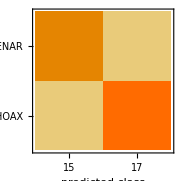
Classifier Measurements
Classifier method | Markov
Number of test examples | 32
Accuracy | (75.8.) %
Accuracy baseline | (53.9.) %
Geometric mean of probabilities | 0.382 ± 0.13
Mean cross entropy | 0.962 ± 0.33
Single evaluation time | 3.87 ms/example
Batch evaluation speed | 724. examples/s
-Graphics- |

```mathematica
evalMarkov = ClassifierMeasurements[classifier, testSet]
```

```mathematica
ClassifierMeasurements[classifier, testSet, "Precision"]
ClassifierMeasurements[classifier, testSet, "Recall"]
ClassifierMeasurements[classifier, testSet, "FScore"]
```

<|BENAR→0.733333,HOAX→0.764706|>

<|BENAR→0.733333,HOAX→0.764706|>

<|BENAR→0.733333,HOAX→0.764706|>

### Fine Tuning

```mathematica
(* Try different methods *)
classifierSVM = Classify[trainingSet, Method -> "SupportVectorMachine"]
classifierRF = Classify[trainingSet, Method -> "RandomForest"]
classifierNN = Classify[trainingSet, Method -> "NeuralNetwork"]
classifierGB = Classify[trainingSet, Method->"GradientBoostedTrees"]
```

ClassifierFunction[…]

ClassifierFunction[…]

ClassifierFunction[…]

«1 more identical outputs»

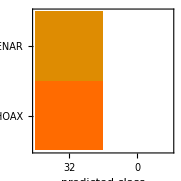
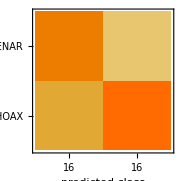
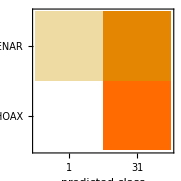
Suport Vector Machine | Random Forest | Neural Network | Gradient Boosting
Classifier Measurements
Classifier method | SupportVectorMachine
Number of test examples | 32
Accuracy | (47.9.) %
Accuracy baseline | (53.9.) %
Geometric mean of probabilities | 0.5 ± 0.00066
Mean cross entropy | 0.694 ± 0.0013
Single evaluation time | 6.56 ms/example
Batch evaluation speed | 636. examples/s
-Graphics- |  | Classifier Measurements
Classifier method | RandomForest
Number of test examples | 32
Accuracy | (66.9.) %
Accuracy baseline | (53.9.) %
Geometric mean of probabilities | 0.504 ± 0.002
Mean cross entropy | 0.686 ± 0.004
Single evaluation time | 9.69 ms/example
Batch evaluation speed | 1.53 examples/ms
-Graphics- |  | Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 32
Accuracy | (56.9.) %
Accuracy baseline | (53.9.) %
Geometric mean of probabilities | 0.505 ± 0.0085
Mean cross entropy | 0.683 ± 0.017
Single evaluation time | 7.3 ms/example
Batch evaluation speed | 847. examples/s
-Graphics- |  | Classifier Measurements
Classifier method | GradientBoostedTrees
Number of test examples | 32
Accuracy | (47.9.) %
Accuracy baseline | (53.9.) %
Geometric mean of probabilities | 0.499 ± 0.0014
Mean cross entropy | 0.694 ± 0.0028
Single evaluation time | 7.59 ms/example
Batch evaluation speed | 1.82 examples/ms
-Graphics- |

```mathematica
evalSVM = ClassifierMeasurements[classifierSVM, testSet];
evalRF = ClassifierMeasurements[classifierRF, testSet];
evalNN = ClassifierMeasurements[classifierNN, testSet];
evalGB = ClassifierMeasurements[classifierGB, testSet];

TableForm[{
  {"Suport Vector Machine", "Random Forest", "Neural Network","Gradient Boosting"},
  {evalSVM, evalRF, evalNN, evalGB}
}]
```

## Interactive Visualization

```mathematica
DynamicModule[{
    selectedModel = "SVM",
    inputText = "",
    result = "",
    showMetrics = False
  },
  
  Column[{
    Panel[Style["Indonesian Text Sentiment Classifier", Bold, 20, Blue], 
      Background -> LightBlue],
    
    Grid[{
      {
        Column[{
          Style["Select Model:", Bold],
          PopupMenu[Dynamic[selectedModel], 
            {"Markov", "SVM", "Random Forest", "Neural Network", "Gradient Boosting"},
            ImageSize -> 200],
          
          Spacer[10],
          
          (* Model Metrics *)
          Dynamic[
            Panel[
              Grid[{
                {"Accuracy:", 
                  NumberForm[
                    Switch[selectedModel,
                      "Markov", evalMarkov["Accuracy"],
                      "SVM", evalSVM["Accuracy"],
                      "Random Forest", evalRF["Accuracy"],
                      "Neural Network", evalNN["Accuracy"],
                      "Gradient Boosting", evalGB["Accuracy"]
                    ] * 100, 
                    {4, 2}
                  ]"%"
                }
              }],
              Background -> LightYellow
            ]
          ],
          
          Spacer[20],
          

          Style["Enter Text for Classification:", Bold],
          InputField[Dynamic[inputText], String, 
            ImageSize -> {400, 100}, 
            Background -> White,
            ContinuousAction -> True
          ],

          Button["Classify Text",
            result = Switch[selectedModel,
              "Markov", classifier[inputText],
              "SVM", classifierSVM[inputText],
              "Random Forest", classifierRF[inputText],
              "Neural Network", classifierNN[inputText],
              "Gradient Boosting", classifierGB[inputText]
            ],
            Background -> Blue,
            BaseStyle -> {FontColor -> White, Bold}
          ],
          
          Spacer[10],
          
 
          Dynamic[
            If[result != "",
              Panel[
                Column[{
                  Style["Classification Result:", Bold],
                  result
                }],
                Background -> LightGray
              ]
            ]
          ]
        }],
        
        Column[{
          Button["Show Model Comparisons", showMetrics = !showMetrics],
          Dynamic[
            If[showMetrics,
              BarChart[{
                evalMarkov["Accuracy"],
                evalSVM["Accuracy"],
                evalRF["Accuracy"],
                evalNN["Accuracy"],
                evalGB["Accuracy"]
              } * 100,
                ChartLabels -> {
                  "Markov ","SVM", "RF", "NN", "GB"
                },
                ChartStyle -> "Pastel",
                PlotLabel -> "Model Accuracy Comparison (%)",
                ImageSize -> 400
              ]
            ]
          ]
        }]
      }
    }]
  }, Spacings -> 2],
  
  Initialization :> (result = "")
]
```